# Real Analysis, Lecture #7

## Plotting Sequences

```mathematica
a[n_]:=(2n)/(3n+2)
```

```mathematica
ListPlot[Table[a[n],{n,1,20}],PlotRange->{0,.75},PlotStyle->PointSize[.02]]
```

```mathematica
DiscretePlot[a[n],{n,1,20},PlotRange->{0,.75},PlotStyle->PointSize[.03]]
```

```mathematica
f[x_]:=3-(1/x)
```

```mathematica
Solve[3-(1/x)==x,x]
```

```mathematica
ListPlot[NestList[f,1,20],PlotRange->{0,3},PlotStyle->PointSize[.02]]
```

```mathematica
(3+Sqrt[5])/2.
```

2.61803

```mathematica
IllustrateLimitDirect[a_,L_,n_,yrange_]:=Manipulate[Show[ListPlot[Table[a[k],{k,1,n}],PlotRange->{L-yrange,L+yrange},PlotStyle->PointSize[.02]],Plot[{L-ϵ,L+ϵ},{x,0,n+1},PlotStyle->{{Thick,Red},{Thick,Red}}]],{ϵ,2,.01}]
```

```mathematica
IllustrateLimitDirect[a,2/3,30,.5]
```

```mathematica
IllustrateLimitRecursive[f_,seed_,L_,n_,yrange_]:=Manipulate[Show[ListPlot[NestList[f,seed,n],PlotRange->{L-yrange,L+yrange},PlotStyle->PointSize[.02]],Plot[{L-ϵ,L+ϵ},{x,0,n+1},PlotStyle->{{Thick,Red},{Thick,Red}}]],{ϵ,2,.01}]
```

```mathematica
IllustrateLimitRecursive[f,1,(3+√5)/2,30,.5]
```

## A Counter-Intuitive Example

### A Simple-Looking Recusively Defined Sequence

Define a sequence x_0,x_1,x_2,x_3,… by letting x_0=.1 and letting x_n=4 x_(n-1)-4 x_(n-1)^2 for integers n≥1.  What is the behavior of this sequence as n gets larger and larger?

```mathematica
f[x_]:=4x-4x^2;
```

```mathematica
NestList[f,.1,500]
```

```mathematica
Manipulate[ListPlot[Transpose[{NestList[f,.1,b],Table[0,{k,0,b}]}],PlotStyle->{Red,PointSize[.02]},PlotRange->{{0,1},{-1,1}},Ticks->{{0,.2,.4,.6,.8,1}, },Axes->{True,False}],{b,0,50,1}]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{Table[k,{k,0,b}],NestList[f,.1,b]}],Joined->True],ListPlot[Transpose[{Table[k,{k,0,b}],NestList[f,.1,b]}],PlotStyle->{Red,PointSize[.025]}],PlotRange->{{0,50},{0,1}},AxesLabel->{"n","x_n"}],{b,0,50,1}]
```

This is an example of "chaos".  Certain statistical/probabilistic patterns are evident, however.

```mathematica
Histogram[NestList[f,.1,100000],AxesLabel->{"x_n","frequency"}]
```

An area of math called Ergodic theory is where the probabilistic patterns in these deterministic situations is studied.

## Any Convergent Sequence is Bounded

## What does it mean for a sequence to “converge to ∞”? (BTW, I prefer to say “diverge to ∞”)

## Algebraic Properties of Convergent Sequences and the Squeeze Theorem

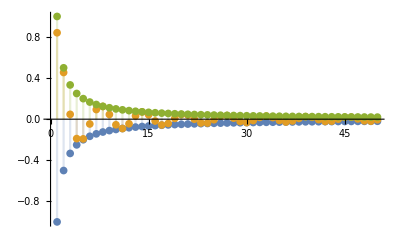

```mathematica
a[n_]:=Sin[n]/n;DiscretePlot[{-1/n,a[n],1/n},{n,1,50},PlotRange->{-1,1}]
```

## Convergent Sequences whose terms all lie in a closed interval [a, b] will have a limit in that closed interval

## A Monotone Sequence Converges iff it is Bounded

## A Recursively Defined Sequence

Let x_(n+1)=x_n^2+.09 for n≥1 and let x_1=0.899999.

```mathematica
f[x_]:=x^2+.09;NestList[f,.899999,50]
```

```mathematica
CobWebPlot[f_,{x_,xmin_,xmax_},{y_,ymin_,ymax_},seed_,iterates_]:=
	Module[{myList},
		myList=NestList[f,seed,iterates]//N;Print[myList];
		Plot[{f[x],x},{x,xmin,xmax},PlotStyle->{{Thick,Red},{Thick,Blue}},
Epilog->Map[{Thick,Line[{{#,#},{#,f[#]},{f[#],f[#]},{f[#],f[f[#]]}}]}&,myList],
	PlotRange->{ymin,ymax}]]
```

## Cauchy Sequences and the Cauchy Convergence Criterion

## Subsequences and the Bolzano-Weierstrass Theorem

## Section 1.4, #4: Let S be a nonempty set of real numbers that is bounded above and let β=sup(S). Suppose that β∉S. Prove that for each ϵ>0, the set {x∈S:x>β-ϵ} is infinite.

## Section 1.5, #30: Let f:[a,b]⟶ℝ be a function and suppose that for each ϵ>0, the function g defined by g(x)=f(x)+ϵ x is increasing on [a,b]. Prove that f is increasing on [a,b].